# Vector RT0 volume PEEC

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

(R+jωL)i+e=Cᵀv; Ci=b

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Choose field or transport excitation. The field case has 1 mT RMS imposed Bz and zero net transport.

## Derivation and interpretation

Lowest-order Raviart–Thomas face-flux degrees of freedom represent a vector current field with cellwise divergence. Adjacent cells share oriented face fluxes; the incidence matrix C enforces discrete current continuity.

The mixed PEEC system is (R+jωL)i+e=Cᵀv with Ci=b. In the imposed-field tutorial Bz=1 mT RMS and net transport is zero; calculate dissipated power from the reconstructed current and resistive quadratic form.

Check the true linear residual, continuity, quadrature and spatial sensitivity. Imposed-field loss is a diagnostic observable; dividing it by a separate transport current squared would not define intrinsic conductor resistance.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"dimensions"->{2,2,3},"cell_width_m"->0.0005,"quadrature_order"->6,"excitation"->"field"|>;parameters
```

<|dimensions -> {2, 2, 3}, cell_width_m -> 0.0005, quadrature_order -> 6, 
 
>   excitation -> field|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"rt0",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_rt0_20261014005950_d9feb598, 
 
>   source_model -> 3D_RT0_volume_face_flux_PEEC, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

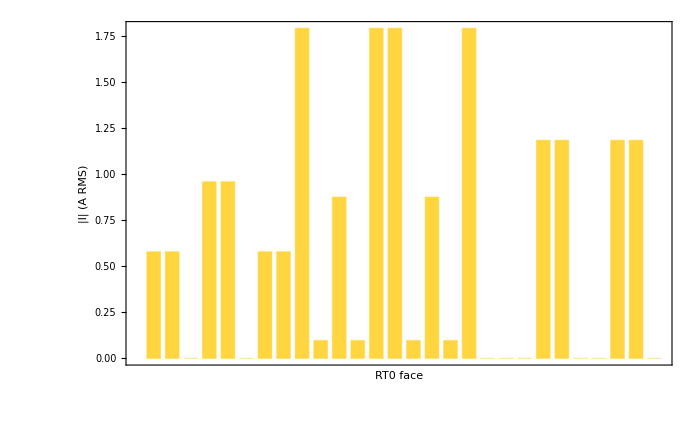

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: P03, RUEHLI1974, RT1977, GMRES1986; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch rt0